I used Mathematica to work through several examples of discrete distributions. I used the most general cases possible. My focus on generalization meant I didn’t include the Bernoulli distribution or the geometric distribution, which are special cases of the the Binomial distribution and the negative binomial distribution, respectively.

## Binomial Distribution

What’s the probability you will have 110 heads out of 2 00 coin tosses?

```mathematica
Probability[x==110,x\[Distributed]BinomialDistribution[200,1/2]]
```

522222081148488803833122500948439092033029510866275025575/25108406941546723055343157692830665664409421777856138051584

```mathematica
NProbability[x==110,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->100]
```

0.02079869433231031517558728371841005445768414097750047505022048008924276263789036205146574846025135596

What’s the probability you will have between 96 and 108 heads out of 2 00 coin tosses?

```mathematica
Probability[96<=x<=108,x\[Distributed]BinomialDistribution[200,1/2]]
```

3911045678877858479058581704940733125002017822953426773745/6277101735386680763835789423207666416102355444464034512896

```mathematica
NProbability[96<=x<=108,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->100]
```

0.6230655235089846805722325124602419646326044754620131215351757111539208666562609916548872155987871016

### different value for p

The probability of getting 10 out of 70 sixes:

```mathematica
Probability[x==10,x\[Distributed]BinomialDistribution[70,1/6]]
```

43010790698981560264968493356718681752681732177734375/369400551818460155582338457473806922708916165381455872

```mathematica
NProbability[x==10,x\[Distributed]BinomialDistribution[70,1/6],WorkingPrecision->100]
```

0.1164340185396338386510498230883484677507515388618920536719888827877847141091800618609411721395454844

The probability of getting between 12 and 60 sixes:

```mathematica
Probability[12<=x<=60,x\[Distributed]BinomialDistribution[70,1/6]]
```

187259069812181268064657770604381223577766417255859375/369400551818460155582338457473806922708916165381455872

```mathematica
NProbability[12<=x<=60,x\[Distributed]BinomialDistribution[70,1/6],WorkingPrecision->100]
```

0.5069268816474554030716964137396395963756543473173258267098037954010037388889134982242586357972781571

### conditional probability

#### fair coin

Find the probability of getting between 96 and 108 heads while tossing a coin 200 times given that between 84 and 120 heads have been scored.

```mathematica
Probability[96<=x<=108\[Conditioned]84<=x<=120,x\[Distributed]BinomialDistribution[200,1/2]]
```

11628989391050479264/18449216239063865589

```mathematica
NProbability[96<=x<=108\[Conditioned]84<=x<=120,x\[Distributed]BinomialDistribution[200,1/2],WorkingPrecision->200]
```

0.63032430431530068809899692345637817699678328822688987423451234841065472237923289930818501311173802387652995237308570370405266806550877430295020304057231993751711686954627743054145416963699253655539679

#### dice

Find the probability of getting between 16 and 18 sixes when rolling a die 200 times given that between 14 and 20 sixes have been scored.

```mathematica
Probability[16<=x<=20\[Conditioned]14<=x<=20,x\[Distributed]BinomialDistribution[200,1/6]]
```

36193145699/36895670699

```mathematica
NProbability[16<=x<=20\[Conditioned]14<=x<=20,x\[Distributed]BinomialDistribution[200,1/6],WorkingPrecision->100]
```

0.9809591481414907345251618026427464239765872157997276145409582597597543675973819434483781302679606291

## NegativeBinomial

The number of tails before getting 150 heads with a fair coin is modeled by the negative binomial distribution with n=150 and p=0.5

```mathematica
𝒟=NegativeBinomialDistribution[150,1/2]
```

NegativeBinomialDistribution[150,1/2]

Make a picture:

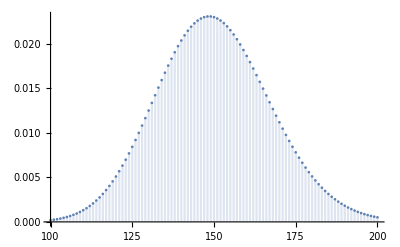

```mathematica
DiscretePlot[PDF[𝒟,k],{k,100,200},ImageSize->Full]
```

Find the probability of getting 144 tails before getting 150 heads:

```mathematica
Probability[x==144,x\[Distributed]𝒟]//TraditionalForm
```

177581905345755788536968927329795127320244431122016245473913189034720070489983603588925/7957171782556586274486115970349133441607298412757563479047423630290551952200534008528896

```mathematica
NProbability[x==144,x\[Distributed]𝒟,WorkingPrecision->150]//TraditionalForm
```

0.0223172139798520103824263061096657053816142787336076491498565735075784938534542633269142347429034257334133198806005769957272081553579779121349985105267

Find the probability of getting between 144 and 156 tails before getting 150 heads.

```mathematica
Probability[144<=x<=156,x\[Distributed]𝒟]//TraditionalForm
```

297857618329631577142510926472452399321226408704586048733051249882573754121758523794407601/1018517988167243043134222844204689080525734196832968125318070224677190649881668353091698688

```mathematica
NProbability[144<=x<=156,x\[Distributed]𝒟,WorkingPrecision->150]//TraditionalForm
```

0.292442177546227742645308199294917938042209286047821489985938298898894428661664174648671978500538827238572356679570434698803903729994502214511203952152

### dice

Investigate the behavior of probabilities until a 6 is rolled 60 times.

```mathematica
𝒟=NegativeBinomialDistribution[60,1/6]
```

NegativeBinomialDistribution[60,1/6]

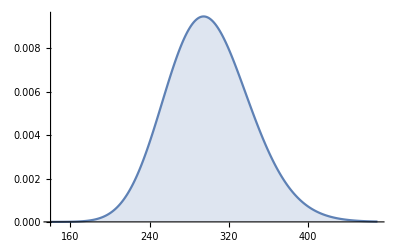

```mathematica
DiscretePlot[PDF[𝒟,k],{k,140,470},ImageSize->Full]
```

Find the average number of rolls needed:

```mathematica
Mean[𝒟]
```

300

Find the probability of needing between 200 rolls and 400 rolls:

```mathematica
Probability[200<=x<=400,x\[Distributed]𝒟]
```

242849610078700433727423260091307804908958805482793279992903925580985060007249275638245059816939076204344209823712956279197244662023245508432257459314383516923308246926820248309248839105935436958296992608018856652170435280643360462492005927256340569324965200292921634779677610620276774677485357970211393424650445408384535905810253098024986684322357177734375/247327652660853136657582802549317307860836151000010160928399335413303654526380251219029844833123749884079069365831121470556071608955707772005518141766714790551099190488887312922073823036667133302676745473036458705631169164059807664647218028456946038541560697004494042933305183130229545409376689763919078773176614442061950620827416361446140111920529057775616

```mathematica
NProbability[200<=x<=400,x\[Distributed]𝒟,WorkingPrecision->500]
```

0.98189429069505140434287598528484891128963732885686008207364192747761748771061299531151199914933059791381728947905891191068620822208529168615793247743602544957086609873587841720966327684300195785182919921609026743444823007962982097212460290810146668994562409081862048045025588032858546123925669948204154550459886645719441994784752015742900484369650404929141670369817216281284705102150277165953556508297351016995992873479608407157217177487860393179683876117527749286176452913264630079930304021728859269

Find the conditional probability of needing 300 rolls given between 200 rolls and 400 rolls are needed:

```mathematica
Probability[x==300\[Conditioned]200<=x<=400,x\[Distributed]𝒟]
```

7463668295930132726957016095102242169311620316559563760547457068240709453412729400212202779631081834290575807202532000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000/780488554937850496930875685014804054589907040883433468008920243582528877616919398404984410604811312307119145942088368203373069259725571799886875171235908504579453835240538389329910106082579702507763373334695136287579

```mathematica
NProbability[x==300\[Conditioned]200<=x<=400,x\[Distributed]𝒟,WorkingPrecision->500]
```

0.0095628158141594491129323341745967670009658079144085290734814635152263905858538358725361290684699469497491163437089394627858840317736058857301588738117342677394055355566440240526771007045414751017115812911559498615898256619724350814880446246821129177830588324502224683626017140180696683282944023148788826101377670908399829761114221479679761722794759547533732022418882565288290997380290786085067727141338848615766928281910854284778206687885985468335487827713254796472147383322052949554079423688118688703

## Pascal Distribution

Investigate the number of trials for the nth success.

If the probability a basketball player makes a free throw is 0.85 we can model this with a Pascal distribution.

```mathematica
85/100
```

17/20

```mathematica
ℬ=PascalDistribution[100,17/20]
```

PascalDistribution[100,17/20]

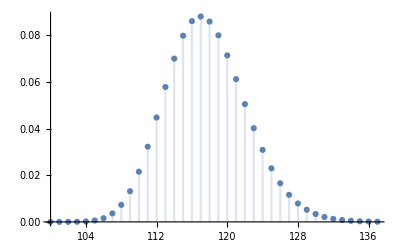

```mathematica
DiscretePlot[PDF[ℬ,x],{x,100,137},ImageSize->Full]
```

Find the probability he needs 108 free throws:

```mathematica
Probability[b==108,b\[Distributed]ℬ]
```

94857722905779789382123716687693390132920034611415847513701323124061536782762016595553918777744723325065677270318922136164936581757961153/12980742146337069071326240823050240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
NProbability[b==108,b\[Distributed]ℬ,WorkingPrecision->100]
```

0.007307573160025131931576501592780196109906675701569703221285782455514243977876551594998488264771416948

Find the probability he needs between 115 and 127 throws:

```mathematica
Probability[115<=b<=127,b\[Distributed]ℬ]
```

12340119534093950561648557166503532958037442796573068857769847640185176834520980936132602486066105356298060174804931766679109525061562926342387658387866907091167893/17014118346046923173168730371588410572800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
NProbability[115<=b<=127,b\[Distributed]ℬ,WorkingPrecision->100]
```

0.7252870400399598697061823206181459729880834426146601146442391480117582256236375838528338166383714723

Find the probability he needs between 16 and 18 throws given he makes 15 free throws within 15 to 20 free throws:

```mathematica
Probability[16<=b<=18\[Conditioned]15<=b<=20,b\[Distributed]PascalDistribution[15,17/20]]
```

828000/1220243

```mathematica
NProbability[16<=b<=18\[Conditioned]15<=b<=20,b\[Distributed]PascalDistribution[15,17/20],WorkingPrecision->100]
```

0.6785533701074294218446653658328709937282983799128534234574588831896597644895320030518511476812405398

Make a plot:

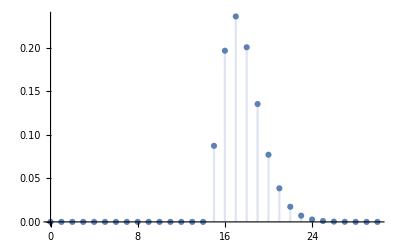

```mathematica
DiscretePlot[PDF[PascalDistribution[15,17/20],x],{x,0,30}]
```

Find the probability he needs between 22 and 24 throws given he makes 20 free throws within 20 to 26 free throws:

```mathematica
Probability[22<=b<=24\[Conditioned]20<=b<=26,b\[Distributed]PascalDistribution[20,17/20]]
```

46097100/75680867

```mathematica
NProbability[22<=b<=24\[Conditioned]20<=b<=26,b\[Distributed]PascalDistribution[20,17/20],WorkingPrecision->100]
```

0.6090984660627632608912897364138283458089876269520009595027498826090351211224892547808681948635710001

Make a plot:

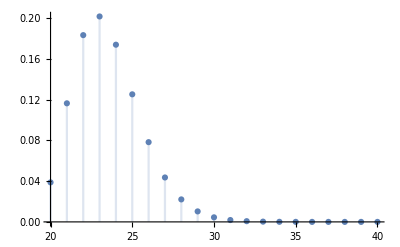

```mathematica
DiscretePlot[PDF[PascalDistribution[20,17/20],x],{x,20,40}]
```

Find the mean number of free throws needed.

```mathematica
Mean[PascalDistribution[20,17/20]]//N
```

23.5294

```mathematica
Mean[PascalDistribution[30,17/20]]//N
```

35.2941

Find the probability he needs 32 to 37 free throws to make 30 free throws if it is given he needs between 30 and 39 free throws:

This took a very long time to run so I am only evaluating it once:

```mathematica
Probability[32<=b<=37\[Conditioned]30<=b<=39,b\[Distributed]PascalDistribution[30,17/20]]
```

1303038921600/1580306483963

```mathematica
%//N
```

0.824548

## Hypergeometric Distribution Examples

### Hypergeometric distribution

There is an urn with 403 marbles in it. 148 of the marbles are white. 54 marbles are drawn from the urn.

```mathematica
urn[n_]=HypergeometricDistribution[n,148,403];
```

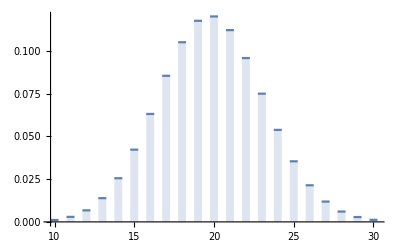

```mathematica
DiscretePlot[PDF[urn[54],k],{k,10,30},ExtentSize->1/2]
```

The probability distribution that there are 21 white marbles elements in a draw of 54 marbles:

```mathematica
PDF[urn[54],21]
```

4160984764936668505747373569589911437037308/37126596243372003987454725483769668696553919

```mathematica
Probability[WhiteMarbles==21,WhiteMarbles\[Distributed]urn[54]]
```

4160984764936668505747373569589911437037308/37126596243372003987454725483769668696553919

```mathematica
NProbability[WhiteMarbles==21,WhiteMarbles\[Distributed]urn[54],WorkingPrecision->40]
```

0.1120755788562089096845237920634821720275

The mean and variance:

```mathematica
Mean[urn[54]]
```

7992/403

```mathematica
Mean[urn[54]]//N
```

19.8313

```mathematica
Variance[urn[54]]
```

118541340/10881403

```mathematica
Variance[urn[54]]//N
```

10.8939

The probability there are between 18 and 20 white marbles given that there are between 17 and 22 white marbles in the sample of 54 marbles:

```mathematica
Probability[18<=WhiteMarbles<=20\[Conditioned]17<=WhiteMarbles<=22,WhiteMarbles\[Distributed]urn[54]]
```

25064549509/46516507129

```mathematica
NProbability[18<=WhiteMarbles<=20\[Conditioned]17<=WhiteMarbles<=22,WhiteMarbles\[Distributed]urn[54],WorkingPrecision->40]
```

0.5388312892773905762790102803722487983025

### Simple Wallenius Hypergeometric

Bob is catching fish in a small lake that contains a limited number of fish. There are different kinds of fish with different weights. The probability of catching a particular fish at a particular moment is proportional to its weight.

Bob is catching the fish one by one with a fishing rod. He is determined to catch exactly 12 fish regardless of how long it may take. He will stop after he has caught 12 fish even if he sees more fish that are tempting.

This scenario of the distribution of the types of fish caught is given by the Wallenius noncentral hypergeometric distribution.

The lake contains 10 red fish with a weight of 2 N and 15 blue fish with a weight of 12 N. Bob catches 12 fish.

```mathematica
𝒟=Block[{m1=10,m2=15,n=12,w1=1,w2=2},WalleniusHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

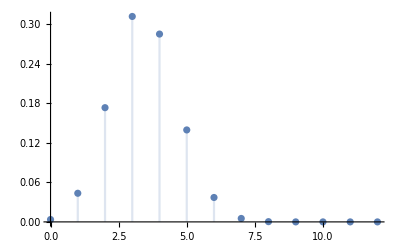

```mathematica
DiscretePlot[PDF[𝒟,x],{x,0,12}]
```

Find the probability at least 3 red fish were caught.

```mathematica
Probability[RedFish>=3,RedFish\[Distributed]𝒟]
```

1155705865/1482664962

```mathematica
NProbability[RedFish>=3,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.7794787727640386500210558020861897186992404289378492779139404792921787545418504332336141089708977691

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

35869458643/10465870320

```mathematica
Mean[𝒟]//N[#,100]&
```

3.427279103053132422149102264053277510895051869895517681132513784099705909598925739412372157120326329

Simulate the number of red fish in 30 consecutive samples of 12:

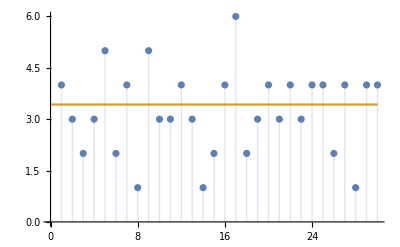

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

### larger example of Wallenius Hypergeometric

Bob wants to catch 403 fish.

The lake contains 570 red fish with a weight of 3 N and 144 blue fish with a weight of 14 N.

```mathematica
𝒟=Block[{m1=570,m2=144,n=403,w1=3,w2=14},WalleniusHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

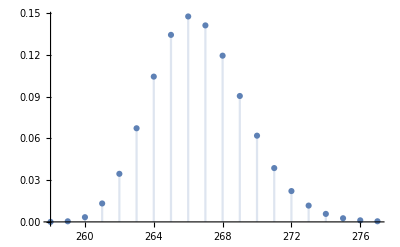

```mathematica
DiscretePlot[PDF[𝒟,x],{x,258,277}]
```

Find the probability at least 260 red fish were caught.

```mathematica
Probability[RedFish>=260,RedFish\[Distributed]𝒟]
```

293080649668889899284068726318069963032701968567369747664449674372964488547971950121144926723974483049487402292402194109389243354935991160244408607298544472990294776400153813183905708210928381667169626770433765479127771679451274900103500875208264736903586314581101473402167102477556252907561932803062283912539645637494929293363401167356298249074245034950878963783965149618729413919845288424709722386172149263141483468788800228986225822936306633166995682114770740002037167852060245997505846787001021501475817696120897704642673339568074514867224463155939828698405265160439126156212353302528145724164631769938372208310110996951297455733919593292759780002013308206706245845603960177634929604326487400873251047705178842745318292551468039684620857840663562371098907922885166834203844801303602440955070973868198965866832986486875555341378087478754643465474552067726090492041837750443655628543583714578786943236771859376993038513595946606791141724296123016666222892683253043354058619289143082026687505005977014793135784059479959314803291465009229309490101133426215935162977818241386990398151029273737208489211983488669292606159935981469691230810759249331615537511166208767058935546824917256608655121780827647832694180434742655618286064788403183273925767136811865960650206043436371978730712741704259270987604267031875653639489087771645700094066312301180480013028236522539414538682036327670233493787658169861900848957465200340216120085102426552791/293206145944026863765288880618440700493520452750354120107019223702913995122561310523279013762494617526946625334450592296283541568147527375753232647985601518604197998947690766754134643123778091709881065843976169257971363184959850002699545613043994730413795355078018121529159832982229290620186824836420098850094316461254689214372246318869875688113311498603053720054630268827301902552505346202488862531329630479766928891774084265716203658043265288376294525076807045754572648319650667378894014332822949503917094153111048613626502636213335467451836344568792155280096832809403734603205689422267076571222879393389908060208821750986629511341815209875679542934808911509014446243144773695353042448955223035744560379426436820539121020175239542776943997804058369122276583942742428235112410544379736684061894684212572107782408255750326748983970640638982195865128229143328446861719755202268471178994113066509013356281092706419138003025734757172484212849139065472165363173681986583679913779014333429893687128914193065378564911666846913018459562118726448228152903304521673850378159196404038856724950094170584764805405020910612622845243132657311409065499634042635116201130140500670865831447570878503824973835532811165343833523163651405490287611642943066350439713380651451931641840867719715326065598173644283473038178102217013733803410998435936212369526081579155683283643045675280404277319932189048792746332095131578582163177978366505374210747843956308500

```mathematica
NProbability[RedFish>=260,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.9995719862053610508026055638289927125435230747665575303257172319264955893857096110449966682596575205

Find the probability between 263 and 270 red fish were caught:

```mathematica
Probability[263<=RedFish<=270,RedFish\[Distributed]𝒟]
```

961547306361782394100135780931678036125128496557215643366745287322863682252106067032399112261890794335966782446401632204733581393109913167272784583799049149743598688378655476232082012603875598397169130452984573863799469107474445099117607422689560576093416782514197770612893331338952830054912080424794573187934400336358967581692316665806356309729032308930556069127757317318781447444392466970037761941468032476067464796921976219650502458688934322864991422891676080463990180176030715219813121718728104821313831560618259214255799369598373020614847704473059082449260846681521932680788806656161292573182778327161522587287011384427336550238247739052409235695971090533434004254708204023029539241842257801740354376801707330992655546673498330443646276515495220441502569582809620753193459082810908295498487716463950212755644246840030515425578048430123748513774349824912455444986892527627902378514796837396479355016444522159694719747412696291089135056595360479718131275665354588346430685728263621564433888507587601580732373844419928015963915938936615819974025307549367585267129983897099629563369855554158475360444719453434904356424067543005298594516443922307489256830224837193740928995303222988728027115680669200312986691496059106063362096626979380741809823352415753323606394360405061221771544240880196726814782933811823093528411115306908792904048416153773866388181212409835929693381381292884764205492937635952762107993298196754783681617359017579/1110587330642784334308454977265754937717941155748642683005003932324843071520951902325261922895639717966210148050433930954220445301612477704100728603241521069840067721435734944437899487624605775203216475493674277555100051901073955454954958083878917057151319653831113624670199842119953758938505913758383603139276637464326746395812928658538605495255301085423724671597270088350839331649695140162333714368531261521857182552487748813714393713625436969082350837838829159497148697454251293640820842134299574536487672920569245488108466708044361389127548385120149429269797016986682351277411672061808151556392318881790392676093330203768973703009131888783360533960188216577708044601632102833855255633408101249827492971051090969364321306253794365118382030086832596438720191980712833084989960902312327715142286831621372851351862709525772456978195236753756564381952049788442954118355629056079569636199381756463833889777971801800047911664208863309048270534633073782513538971410859568733943422928863607791236276007850408225692767042422729283174903669607613133071314265734919840460577166093243269095460236529709310267452911064139920120735773146105763902054607404758493659285781580537474663875955576557843375136574731403337411276440330050538359265951748674984379866294068164039081783354205338555589717108218816295404468945051674859758065924282617341474694104373571343176480041098279884860426302838785067633450653132410880162871559460272149704915224668125

```mathematica
NProbability[263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->400]
```

0.8658007162797897730766004810516498234119074203575403128097836147770559202243301757223195790447678380656624004964297680965332299585338040221283349263789410473617296802095580954879203663785390005882786719317918086418180160001288079482988700540864228475778215646078183219744322349701246306642607891160732899677111046405097809225710098960056105096663023954129639076671530060114691761617824169274819775573

Find the probability between 264 and 268 red fish were caught given between 263 and 270 fish were caught:

For some reason Probability won’t evaluate. I’m not sure if its a computational limitation. I hope its something that could be implemented with software and not a hardware or memory limitation.

```mathematica
Probability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟]
```

Probability[264≤RedFish≤268\[Conditioned]263≤RedFish≤270,RedFish\[Distributed]WalleniusHypergeometricDistribution[403,570,714,3/14]]

This will evaluate:

```mathematica
NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->200]
```

0.6463378475216264030065819635244471734736956273586213410616800035264447199906946210443089700984366497374080814998979796368978897640617255056564350001812912211267259815273237139735068207698188913965963

It does work to ask for an exact probability however:

```mathematica
Probability[264==RedFish\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟]
```

75737960682467920848591319967218466985124221401710303739963530510458748204195290253382341417887575127953467187546326213019468251605850022085312702197774705232897844200330706034044839833588186662173902131159639634213634725427291346677396438089630683366814759794493908284715835447332658201337746980404362287727224406902838999653844068272373052377571421634182333628376223017795080702084792607635237412761343964780836625648818255397350340824828061233767163203604352042659871194221276005526039146462403373378881370732207686038775109394898232920657726194366295448120498532137834972972381004787035804162401017827314642435332523061392235388177005214183169724291441255228862106742243085829911508941833632848303963036444216012672822901111192505430270905807481206328115314260704262834715803681464300994315350356413882744282674937628297667841400567660616884404849187994991716075787814439495156369575020532647009406119811675776483933329323915934483469453586679799575557629335974953272746997534417380642377142715155627035957494080239339093608036412624456893524115018976411758001237951415822328701461001843147563636042249082679863652362571951414226492723744038681745410253354635824370147972347062678546385421556009791325403376495688453213974962914238641473370922026049606774363687559686991497148984431521581800254604675519074467014559511929840378625780952982306431258328329576147342711870966022273370869809232147562911913155091738433326950233081563858853/628834495079893094534114139111207013072164611882171626624546398642532117933402146534761727446648504631734885223949611612567879176828611020295563831233536831604075940014983896832494496501635573862019941543857214910711661617186731783762525627983191994877460655752794098505782247053270016049643335432187663042229294164941677047014870596566011130972266975200951238840299249590923818875050865264637690554264028298139260358952346595463105934078805422542326220022526797767229329675235823985290132036431649260195445105221101014604025724765391692039144878671248790624658922631538924251414853412524229909835702386266658532070319168363884548792761812001009449960720355029082640712192122273782703705762815576591027796563002219834797874843564873379868447708681029692067629023923370017778238955999197962581579951748003642411571206872958408365738351496873072381697358005738175618167721471976034285995669708300585291625694700865052435633131358760952253160732339066069490573255803070120681299413844718312371101241027111534773113574567370769380055087110612234133771332199312829138649149420544573729896313414476632236205997891579441193371606733702994987509673519840197522612561447333293813502131885995878700413951988689371876350789709318405880929357700070646800026570332326455465612826691724099336425965240123959430049201523935829531743339924570247763117235793300417621533780839954051981760929348376139514669892834988104909365714269014566271983641203716178088

I am trying to compute it manually:

Find the total of probabilities for i=264 to 268:

```mathematica
Total[Table[Probability[RedFish==i\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟],{i,264,268}]]
```

234718871418641210689583685572738002369157989311844749001407382157437366739040032895221193826618151717297835757033568081572410851550491078401835827302469122019636625615011294387685083270557445905755166222257247898798046121713838219627188405503954966077281831114869172104655084359219176651439416207038616900061201793264536601254281991522426069684165319697068463987606390429693461490318105849164973748498324486748493930647056184886580015039466218786282894864040607947743120244820250081597482508520849853016015861139040700850885660906281418436749785408718616115352772629538280098694037530007972670449510578039948450343695787962177972564082779378180486546467089534722714342200986394023547860092235362807010950934182340575869176194320445255496752918935024299702629339151837978895249822722492683851259623605879886342420452764668472704596047192274956329713264769003301529570601114303522332774906640726085857754368217074120662992868288392250921824269318991846623523191625640486067335345007244469583425983156618127341154485480101145336827930696069704240555815647791529694169995499785307007907912426074554704840374417677636049637200808474337266116735331569701994389992889450467260336430752684512043471861310319759604990255346507163907408481709998516374631017122544969088793441010195448080912171981934345370415955105515044497867057513227301699467643340506342546470699947231869575438962970041057456732630165873180048397675095127451788361098188004842279/314417247539946547267057069555603506536082305941085813312273199321266058966701073267380863723324252315867442611974805806283939588414305510147781915616768415802037970007491948416247248250817786931009970771928607455355830808593365891881262813991595997438730327876397049252891123526635008024821667716093831521114647082470838523507435298283005565486133487600475619420149624795461909437525432632318845277132014149069630179476173297731552967039402711271163110011263398883614664837617911992645066018215824630097722552610550507302012862382695846019572439335624395312329461315769462125707426706262114954917851193133329266035159584181942274396380906000504724980360177514541320356096061136891351852881407788295513898281501109917398937421782436689934223854340514846033814511961685008889119477999598981290789975874001821205785603436479204182869175748436536190848679002869087809083860735988017142997834854150292645812847350432526217816565679380476126580366169533034745286627901535060340649706922359156185550620513555767386556787283685384690027543555306117066885666099656414569324574710272286864948156707238316118102998945789720596685803366851497493754836759920098761306280723666646906751065942997939350206975994344685938175394854659202940464678850035323400013285166163227732806413345862049668212982620061979715024600761967914765871669962285123881558617896650208810766890419977025990880464674188069757334946417494052454682857134507283135991820601858089044

```mathematica
Total[Table[Probability[RedFish==i\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟],{i,264,268}]]//N[#,200]&
```

0.74652034280918479362280193636112156066451397224997296035475500696811703208457771356774509850368929876435533739937087357412551459283344388357025825488428961250426954754422546257946203798054767301788558

For some reason I have a different answer than the numerical result:

```mathematica
NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->200]
```

0.6463378475216264030065819635244471734736956273586213410616800035264447199906946210443089700984366497374080814998979796368978897640617255056564350001812912211267259815273237139735068207698188913965963

Here is the difference

```mathematica
(Total[Table[Probability[RedFish==i\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟],{i,264,268}]]//N[#,100]&)-NProbability[264<=RedFish<=268\[Conditioned]263<=RedFish<=270,RedFish\[Distributed]𝒟,WorkingPrecision->200]
```

0.100182495287558390616219972836674387190818344891351619293075003441672312093883092523436128405252649

Event B is 263<=RedFish<=270. Event A is 264<=RedFish<=268. We are given event B and want to find the probability of A | B.

P(A|B)=(P(A∩B))/(P(B))=(P(263<=RedFish<=270∧264<=RedFish<=268))/(P(263<=RedFish<=270))=(P(264<=RedFish<=268))/(P(263<=RedFish<=270))(*because 263<=RedFish<=270 is already true if 264<=RedFish<=268 is true*)=∑_(i=264)^268 P(RedFish==i,i\[Distributed]𝒟)

Here I tried computing the probability with Table but got a different result from the correct answer of 0.646:

```mathematica
1/Probability[263<=RedFish<=270,RedFish\[Distributed]𝒟](Table[Probability[i==RedFish,RedFish\[Distributed]𝒟],{i,264,268}]//Total)//N
```

0.74652

Please comment if you have any ideas on how to find the exact conditional probability for Wallenius noncentral hypergeometric distribution.

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

2562721882021945273935552423289638978380853575362046001914347508970196492756426452026967505362852371768407654433426496590333501317521502519894824084416337290556115378215945756570887867463790797207824779899222787789125982571442320101718175661332726678607969219005690290464812882647806702816554257562598062995341043471037165318142348928360558842076145220249374869739862316107474119802762089596370035889876864028137220141703867728614817550869446486631828007617068529023681204402109929880937445993987431466784119770193386179643468389717200871254419662507157146052398860551233406303262478377640770986566320916362764897413022043730729962142955798740176912736120340258406254858774001624373341214156407508955921201995525572735868103947575011387726161594377962787840796504401109765546665869153346894810773835132728643774348697286449580038814694532891433113706756006748239056029010427177035556853988586425065565557522225588375197114201574818059089563195854966279847116804819395224371749266309389248947814305542358062080205517383108403360113201703103864340761729603344886020854804097183434521693577732556817642722236876968306082773222954942897047447769031555312088005348395407791357655504466220412550056811290295979538861451682986615936611788529273376954414116000046974509334192631874441357524169508179747183325651134863336496733965390113269994561105545784279032603512657592958746453242492809250796607982867857033555361664838882869307741287822653396731621490168773204610218885389734751285920687533082449332239/9611771445207769155336871027194752755072897276482225878839220633187483296792911122399648924371505054979060541638063804836916830885202165729328297648116637046347746247174925582148720692468764383845644442016737506408208256167676861590602410902216436811638753755109236960745813767595706582457308176381492456077570135590779104903649416490133093141706990270189255192375752119603585261318035236306792094069702115622525616183658640948316068208358703146693017196982056084551470213201081599646817912657933343776487045575353173464427880673684134537683795247376669257193933027371410615471321296204617181340443664830485993507635657219114178762095677602152462090666044880726182614334573605011366994188078543406329214798143992460455232468743364256198343852046239730425205972986416907979440614597500916579282928438469655552776468943173765628679763294652069576737497869413683053145636368180911076164346643860496950947685509181089453376935593684529123926547513931492736767105919858188884665371480918293202193638391522739282604121799733718198270301832733745976366030832868168431186236050648008128523561287979097225361678840462664024202448153214259379360410728316960041091885735930365553905592263260195675452768666792491483324751755318234256403568831034513243392101099895100014861940401201488165736020141222397112404393600831547579495903387736250174718251126502325179046124202912964265319637893951365783065430763817068123859794545755735636714413439989415809956743302991389018266642817013094598801425316784474430000

```mathematica
Mean[𝒟]//N[#,100]&
```

266.6232646740331624105809717002540336430673865987875701022154512267191750654823415590956085619225586

Find the variance:

```mathematica
Variance[𝒟]
```

210829688541117055742370356522311545227171406633600108097280857626646078530602928282008509399198979629210361338200043984026199702716443213428290309261708627839738275429438957414139775616663522693530494029294993286585984231760822327801369746435212441898496931262907069724077270179079919520101572843767584942196480938500085236771313987497537468513732645146520730090639400633175350410638963831967220958088659045576003685035568760276102594644619515468900109179093573953285909887265313772478840297811707126960830061316967851047015420901216364374875832785462429378040981609068455441347854944395215143546785127933573373489879841417626630393505425675279719097611608580546175192087528414569473384282165112571486143732640471121029363987120725677097831066117812529912911386730508525847955364804798244454292854634399651254020126980007992183022598676119883542967227920930731393482610688449772710228157685168093668840698101150084520910042980709529640085900308153254098342128472574780291049396124091313438492965354982991796761859109680234272738850810904343987193676753785704673318459910913487767823812497451760812942300038017412121399836484750721948472191874091771853786363001459392822176615034952044207689127178220214184211126459212344371984493228326196407812206157550553274241509326032302847265135431359310182843545811467457476959602284621517131642097625671913803360035689361377624053278603898089587414112717188772405551317429581727349129588544240317720940202437304340019216767282934903249568955975689155149672069990577745565076525259854278056735310954049809389105182784233167755857893548900848910876789133780595533873050248801176064289036947680640480630272079465166717585253482030688968399306906170559326948756395384625960601584427244841776932328404187100170204772606931148529753377515039606351361064621191651285877966508385498003066334795481187779957974934236033940559948517951011479843343996160772641917254705052388341286925901505479506659771568574206424605148983440503732318327568824422928104316059325965041146069847680758765202348261999410077274003858562191086750239136636548822384954792522076687704167278647121587137465395038143311583192714513161262743898101132129009530702406754815489543268286151903334432078503581535355500874191923725115991409848968190173293064549344895410550329620624738480245110473954607543192899208737211919999990688402745483271562027201798449927470707475536130272788623703392665445458217942893531709436674073554253729024263665654232557309182011329511618624799326324521411663399789499032772903921144604670945877391242805686927374965527451408711457472315319544164903787993291572523639240780085831213945856684247195913201280488132906465244808179849337672850810942607888036179414218110765252802802168504531099828135346875489194687678578525098610881444537212809329822267553658028234462223673635004986104733378275232467873382916396836710980618382008207420113834714838336572941274276747569663343488286924698614338426887440315868006295671743975492530375312065993823013354507273974409369/28732092747937460108396860570203271754697283923375940055935454777417267622585904057052552519976141340268117643165985911057094615658023202321448092713930017023462567919297528917324116075859261714321302692255249063937556516066512133614910532019578375842665103777534454494282577250483073897024182786246105341322882099751154223404032102974836136742338967299604012713094762856680349710422287406437150090157362572921358324767411261202791210834998210409745318405412960589121775350351480747558143276956766683944963429908660493641550365393544136595273341206017776100483684531877199823076594274690736405099970479872950969928305772154495573250875237062165209160340504433415205371933190358834409991691364509828483896253448369973427501462092067357652545069229121975890509117786841010762361157261464018760814284695051842090007780748040559410816947558764909577058487471978035954838039723191255033061667120953417865007520369326826778115325460282995783376688755105717413228109755342169213591969748686010794037834090825501662828792813555850797068965689702252404356948703854174473912613867174958763540115915308988912798947570512355760510769227216980653277607550539782891601194531481591038533359429276711167398610344307272771648628753902848967109754874040318526745698107108981412414489629653342874067766162867731011892105335686759833941927118974194603053656575915564574868366941655008339318145704696550795876669833368750827557968367655382491092547576277750131734054881657335116336015066328018302327087430263396208440595037024248020388995049365664299084316451957553100763933548543468574443889266318289395806118752183732606837781919007273505397401705055277568653876292304618018782998716144220766277182795834837376070486708587037945031584052713742369929132976279023078547425169867475952935940405716835485648283593657723074515618965913392465786252925337308305378673539024924201230383863946507135684785108835144805680884804252029396381284281791447880244777642418135715407140773274300990071544127655069622190115216578828232180441367758370771842683504674577030875119179201499864881571367123648158616433944878062951984117049003547660381968596071131975891641196883548799921326441104257900713951214519527131907128314107437425291105421706639925424773913997971847392981659769421937563037837290302291093178454742685642824931874971664399824316579645023819216381909743230454850802612714464644925157327311723964096382677779857637707120639215089997770678010191956555582065246986414994291804149942019969996496166285347648515707750430629568199251638881296103487277134892987324540243088204399757327809326110975556554518960419660883156908054945304483047937903997014325718139248871656746635037170277433568185693602601096715751378294788682967055159345095535731925965462461294701185727763135828973792013354431812685237912068725065260617492188657095672087936100812885068495860019780743622569598289068926280438896607862816609590593796625170144734692534305714296383350159948762028494781004329656758800325035066929956438106201709543900000000

```mathematica
Variance[𝒟]//N[#,200]&
```

7.3377769726241578231051269177734952263284806520005346341994039775333855340079517054282703309586017703471925125414194642273989519224340688217118886871256722960623673034641844795753691956430159561293772

Simulate 30 catches of fish:

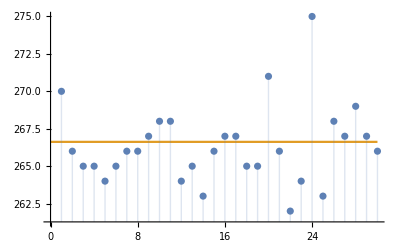

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

I would like to model a multivariate case with red fish blue fish and green fish but the multivariate Wallenius noncentral hypergeometric distribution is not implemented.

The cases above could also be interpreted as marbles in an urn, for example.

I tried finding the moment generating function for the Wallenius distribution but it didn’t evaluate. I found a paper that discusses the MGF for the Wallenius hypergeometric distribution when I Googled something but I didn’t have access. The paper has the Wallenius hypergeometric as a special case.

```mathematica
MomentGeneratingFunction[WalleniusHypergeometricDistribution[5,12,20,4],t]
```

MomentGeneratingFunction[WalleniusHypergeometricDistribution[5,12,20,4],t]

```mathematica
Moment[WalleniusHypergeometricDistribution[5,12,20,4],2]
```

546979898266/29945045845

```mathematica
CharacteristicFunction[WalleniusHypergeometricDistribution[5,12,20,4],t]
```

CharacteristicFunction[WalleniusHypergeometricDistribution[5,12,20,4],t]

```mathematica
Expectation[Exp[t x],x\[Distributed]WalleniusHypergeometricDistribution[5,12,20,4]]
```

Expectation[ⅇ^(t x),x\[Distributed]WalleniusHypergeometricDistribution[5,12,20,4]]

```mathematica
MomentGeneratingFunction[HypergeometricDistribution[5,12,20],t]
```

(7+105 ⅇ^t+462 ⅇ^(2 t)+770 ⅇ^(3 t)+495 ⅇ^(4 t)+99 ⅇ^(5 t))/1938

### Simple Fisher hypergeometric

You are catching fish as in the example with Bob, but using a big net. You set up the net one day and come back the next day to remove the net. You count how many fish you have caught and then you go home regardless of how many fish you have caught. Each fish has a probability of being ensnared that is proportional to its weight but independent of what happens to the other fish.

The total number of fish that will be caught in this scenario is not known in advance. The expected number of fish caught is therefore described by multiple binomial distributions, one for each kind of fish.

After the fish have been counted, the total number n of fish is known. The probability distribution when n is known (but the number of each type is not known yet) is Fisher’s noncentral hypergeometric distribution.

```mathematica
𝒟=Block[{m1=10,m2=15,n=12,w1=1,w2=2},FisherHypergeometricDistribution[n,m1,m1+m2,w1/w2]];
```

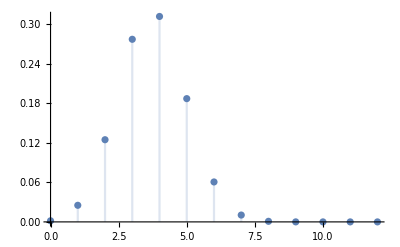

```mathematica
DiscretePlot[PDF[𝒟,x],{x,0,12}]
```

Find the probability at least 3 red fish were caught.

```mathematica
Probability[RedFish>=3,RedFish\[Distributed]𝒟]
```

6720275/7921683

```mathematica
NProbability[RedFish>=3,RedFish\[Distributed]𝒟,WorkingPrecision->100]
```

0.8483392986061169072279211374653593182155862586271124456760009205114620213911614488991796313990347758

Find the average number of red fish caught:

```mathematica
Mean[𝒟]
```

3286802/880187

```mathematica
Mean[𝒟]//N[#,100]&
```

3.734208753367182201055003084571801219513580636841943814212207178701798595071274626869063051374310232

Simulate the number of red fish in 30 consecutive samples of 12:

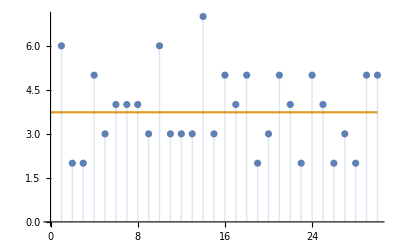

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->{1->Axis}]
```

Compute the variance:

```mathematica
Variance[𝒟]
```

1160420233804/774729154969

```mathematica
Variance[𝒟]//N[#,40]&
```

1.49783989199481338307429415751793040354

Compute a conditional probability

```mathematica
Probability[3<=RedFish<=5\[Conditioned]2<=RedFish<=7,RedFish\[Distributed]𝒟]
```

448/561

```mathematica
NProbability[3<=RedFish<=5\[Conditioned]2<=RedFish<=7,RedFish\[Distributed]𝒟,WorkingPrecision->40]
```

0.7985739750445632798573975044563279857398

Do another simulation of 30 consecutive samples of 12:

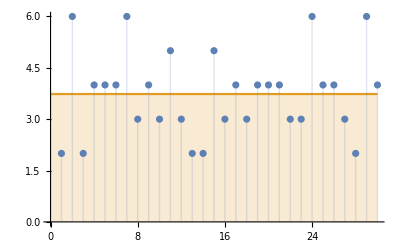

```mathematica
ListPlot[{RandomVariate[𝒟,30],{{0,Mean[𝒟]},{30,Mean[𝒟]}}},Joined->{False,True},Filling->Axis]
```

### Multivariate hypergeometric

An urn contains 12 red glass marbles, 23 blue glass marbles, 11 yellow glass marbles and 9 green glass marbles. Find the distribution of a sample of 28 marbles drawn without replacement:

```mathematica
𝒟=MultivariateHypergeometricDistribution[28,{12,23,11,9}]
```

MultivariateHypergeometricDistribution[28,{12,23,11,9}]

Find the probability of getting a range for each color:

```mathematica
RandomInteger[{3,10},{30,2}]
```

{{7,8},{9,10},{8,9},{7,7},{6,4},{5,10},{9,9},{7,9},{9,7},{3,10},{4,6},{8,10},{5,4},{4,9},{5,10},{9,5},{4,8},{9,10},{3,4},{9,3},{5,3},{10,5},{7,8},{6,10},{10,6},{5,4},{9,10},{10,6},{3,5},{3,4}}

```mathematica
Probability[And[7<=RedGlassMarble<=8,3<=BlueGlassMarble<=10,4<=YellowGlassMarble<=7,4<=GreenGlassMarble<=9],{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

2578551855957/24833411041430

```mathematica
Probability[7<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

13005/32374

```mathematica
NProbability[7<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

0.401711

```mathematica
Probability[7<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10&&3<=BlueGlassMarble<=10,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

175168278387/335567419415

Add a conditional probability:

```mathematica
Probability[7<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10&&3<=BlueGlassMarble<=10&&4<=YellowGlassMarble<=7,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

2247384951/4007267641

Unfortunately I wasn’t able to compute multiple conditional probabilities with intervals. Probability didn’t evaluate and NProbability didn’t evaluate in a reasonable amount of time so I aborted the calculation:

```mathematica
Probability[6<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10&&(Conditioned[6<=BlueGlassMarble,5<=BlueGlassMarble<=10])&&4<=YellowGlassMarble<=7&&4<=GreenGlassMarble<=9,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]
```

Probability[6≤RedGlassMarble≤8\[Conditioned]5≤RedGlassMarble≤10&&(6≤BlueGlassMarble\[Conditioned]5≤BlueGlassMarble≤10)&&4≤YellowGlassMarble≤7&&4≤GreenGlassMarble≤9,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]MultivariateHypergeometricDistribution[28,{12,23,11,9}]]

```mathematica
NProbability[6<=RedGlassMarble<=8\[Conditioned]5<=RedGlassMarble<=10&&(6<=BlueGlassMarble<=8\[Conditioned]5<=BlueGlassMarble<=10)&&4<=YellowGlassMarble<=7&&4<=GreenGlassMarble<=9,{RedGlassMarble,BlueGlassMarble,YellowGlassMarble,GreenGlassMarble}\[Distributed]𝒟]//StandardForm
```

$Aborted

## Beta binomial

b black balls are sampled without replacement b

```mathematica
PolyaEggenbergDistribution[w_,b_,c_,n_]:=BetaBinomialDistribution[w/c,b/c,n]
```

The distribution models an urn scheme. An urn contains w white balls and b black balls. When a ball is drawn it is returned to the urn together with c additional balls of the same color. The distribution gives the probability of drawing k white balls in n draws:

There are 20 white and 24 black marbles in the urn. We return 3 additional balls of the color we observe. We conduct 10 draws.

```mathematica
𝒟=PolyaEggenbergDistribution[20,24,3,10]
```

BetaBinomialDistribution[20/3,8,10]

```mathematica
Mean[𝒟]
```

50/11

```mathematica
Mean[𝒟]//N
```

4.54545

```mathematica
Variance[𝒟]
```

22200/5687

```mathematica
Names["*Dirichlet*"]
```

{DirichletBeta,DirichletCharacter,DirichletCondition,DirichletConvolve,DirichletDistribution,DirichletEta,DirichletL,DirichletLambda,DirichletTransform,DirichletWindow}

```mathematica
Names["Multivariate*Distribution"]
```

{MultivariateHypergeometricDistribution,MultivariatePoissonDistribution,MultivariateTDistribution}

## Summary

There are several hurdles I encountered. I would like to be able to:

evaluate conditional probabilities with the pascal distribution faster. I think this might be a computational limitation with computing the binomials unfortunately.

evaluate multivariate Wallenius and Fisher hypergeometric distributions.

evaluate conditional probabilities with Wallenius hypergeometric exactly. NProbability worked but Probability was not able to give an exact answer for a large problem.

evaluate multiple conditional probabilities with the hypergeometric distribution.

## Multivariate Fisher Distribution

```mathematica
c=3;
m=RandomInteger[{8,14},3]
```

{10,12,14}

```mathematica
totalNumber=Total[m]
```

36

```mathematica
weights={1,2,3}
```

{1,2,3}

```mathematica
?ProbabilityDistribution
```

```mathematica
Transpose[{m,weights}]
```

{{10,1},{12,2},{14,3}}

```mathematica
f@@@Transpose[{m,weights}]
```

{f[10,1],f[12,2],f[14,3]}

```mathematica
f=Binomial[#1,x]#2^x&
```

Binomial[#1,x] #2^x&

```mathematica
f@@@Transpose[{m,weights}]
```

{Binomial[10,x],2^x Binomial[12,x],3^x Binomial[14,x]}

5+2

{7.}

utils:::menuInstallPkgs()

dMWNCHypergo(c(8,10,6),c(20,30,20),24,c(1.,2.5,1.8))

REvaluate::rerr: Failed to retrieve the value for variable or piece of code dMWNCHypergo(c(8,10,6),c(20,30,20),24,c(1.,2.5,1.8)). The following R error was encountered: Error in dMWNCHypergo(c(8, 10, 6), c(20, 30, 20), 24, c(1, 2.5, 1.8)) : 
  could not find function "dMWNCHypergo"

$Failed

library("BiasedUrn");
dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))

REvaluate::rerr: Failed to retrieve the value for variable or piece of code library("BiasedUrn");
dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8)). The following R error was encountered: Error in typeof(myRandomVar123456748678) : 
  object 'myRandomVar123456748678' not found

$Failed

install.packages("BiasedUrn")

library("BiasedUrn")

{BiasedUrn,stats,graphics,grDevices,utils,datasets,methods,base}

dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))

{0.00359094}

```mathematica
ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); 2+2}"]
```

{4.}

```mathematica
ExternalEvaluate["R","cat(\"12\")\; cat(\"13\"); cat(\"\\n\")"]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code cat("12")\; cat("13"); cat("\n"). The following R error was encountered: Error in typeof(myRandomVar123456735950) : 
  object 'myRandomVar123456735950' not found

$Failed

```mathematica
ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\");dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))}"]
```

{0.00359094}

```mathematica
ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\");dWNCHypergeo(12, 25, 32, 20, 1)}"]
```

{0.0451952}

```mathematica
Probability[x==12,x\[Distributed]WalleniusHypergeometricDistribution[20,25,25+32,1]]
```

15283000/338155741

```mathematica
NProbability[x==12(*the 12 in dWNCHypergeo(12, 25, 32, 20, 1) corresponds to there being 12 red balls in the sample of 20*),x\[Distributed]WalleniusHypergeometricDistribution[20(*the 20 in dWNCHypergeo(12, 25, 32, 20, 1) corresponds to there being 20 balls sampled*),25(*the 25 in dWNCHypergeo(12, 25, 32, 20, 1) corresponds to 25 red balls in the urn*),25+32(*the total number*),1(* the odds ratio this represents the ratio of the weights for example the weight of fish 1 by the weight of fish 2 would be 2 kg/12kg*)]]
```

0.0451952

dWNCHypergeo (x(*number of red balls sampled. There are 12 in the example.*), m1(*initial number of red balls in the urn. There are 25 in the example*), m2(*initial number of red balls in the urn. There are 32 in the example*), n(*total number of balls sampled. There are 20 balls sampled in the example.*), odds(* probability ratio of red over white balls. This is 2.5 in the example.*), precision = 1 E - 7)

```mathematica
12/(20-12)//N
```

1.5

```mathematica
7+9+11
```

27

```mathematica
ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\"); dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))}"]
```

{0.00359094}

```mathematica
ExternalEvaluate["R","{ dMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))}"]
```

{0.00359094}

```mathematica
ExternalEvaluate["R","{ pWNCHypergeo(c(8,10,6), c(20,30,20), m2, n, odds, precision=1E-7, lower.tail=TRUE)}"]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code { pMWNCHypergeo(c(8,10,6), c(20,30,20), 24, c(1.,2.5,1.8))}. The following R error was encountered: Error in pMWNCHypergeo(c(8, 10, 6), c(20, 30, 20), 24, c(1, 2.5, 1.8)) : 
  could not find function "pMWNCHypergeo"

$Failed

There are 8 red fish 10 blue fish and 6 green fish

## Evaluating probabilities with the multivariate Fisher distribution

I have the following numbers of fish

```mathematica
SeedRandom[1]
fish=RandomInteger[{40,100},5]
```

RandomGeneratorState[…]

{92,60,41,88,42}

I would like to find the following probabilities:

```mathematica
probabilityVector={RandomInteger[{20,92}],RandomInteger[{20,60}],RandomInteger[{20,41}],RandomInteger[{20,88}],RandomInteger[{20,41}]}
```

{32,27,28,48,36}

I have the following weights:

```mathematica
weights=RandomReal[{1,E^2},5]
```

{1.53869,4.94664,1.52275,2.79674,2.77884}

```mathematica
numberOfFish=Total[probabilityVector]
```

171

```mathematica
ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\"); dMWNCHypergeo(c(32,27,28,48,36),c(92,60,41,88,42) , 171, c(1.5386946376145794,4.946642504228828,1.5227528640809576,2.796741031424972,2.778843627609227))}"]
```

{1.00981×10^-17}

```mathematica
ToString[probabilityVector]
```

{32, 27, 28, 48, 36}

```mathematica
RForm//ClearAll
RForm[string_?StringQ]:=StringReplace[string,{"{"->"(","}"->")"}]
```

```mathematica
RForm[ToString[probabilityVector]]
```

(32, 27, 28, 48, 36)

```mathematica
RForm[ToString[weights]]
```

(1.53869, 4.94664, 1.52275, 2.79674, 2.77884)

```mathematica
RForm[ToString[fish]]
```

(92, 60, 41, 88, 42)

```mathematica
RForm[ToString[Total[probabilityVector]]]
```

171

```mathematica
StringRiffle[{RForm[ToString[probabilityVector]],RForm[ToString[fish]],ToString[Total[probabilityVector]],RForm[ToString[weights]]},","]
```

(32, 27, 28, 48, 36),(92, 60, 41, 88, 42),171,(1.53869, 4.94664, 1.52275, 2.79674, 2.77884)

```mathematica
StringJoin[{"dMWNCHypergeo",StringRiffle[{RForm[ToString[probabilityVector]],RForm[ToString[fish]],ToString[Total[probabilityVector]],RForm[ToString[weights]]},","],")"}]
```

dMWNCHypergeo(32, 27, 28, 48, 36),(92, 60, 41, 88, 42),171,(1.53869, 4.94664, 1.52275, 2.79674, 2.77884))

```mathematica
ToRForm[weights]
```

RVector[double,{1.53869,4.94664,1.52275,2.79674,2.77884},RAttributes[]]

```mathematica
ExternalEvaluate["R",ToRForm[weights]]
```

ExternalEvaluate::keyinvalid: Command RVector[double,{1.53869,4.94664,1.52275,2.79674,2.77884},RAttributes[]] is invalid.

$Failed

```mathematica
ExternalEvaluate["R",StringJoin[{"{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\"); dMWNCHypergeo",StringRiffle[{RForm[ToString[probabilityVector]],RForm[ToString[fish]],ToString[Total[probabilityVector]],RForm[ToString[weights]]},","],")"}]]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code {install.packages("BiasedUrn"); library("BiasedUrn"); dMWNCHypergeo(32, 27, 28, 48, 36),(92, 60, 41, 88, 42),171,(1.53869, 4.94664, 1.52275, 2.79674, 2.77884)). The following R error was encountered: Error in typeof(myRandomVar123456774010) : 
  object 'myRandomVar123456774010' not found

$Failed

```mathematica
MultivariateWalleniusHypergeometricDistributionPDF[probabilityVector_,totalNumberVector_,sum_,weights_]:=ExternalEvaluate["R","{install.packages(\"BiasedUrn\"); library(\"BiasedUrn\"); dMWNCHypergeo(c(32,27,28,48,36),c(92,60,41,88,42) , 171, c(1.5386946376145794,4.946642504228828,1.5227528640809576,2.796741031424972,2.778843627609227))}"]
```